# Final Exam

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

## Problem 12

A charged particle of mass m = 0.03 kg and charge q = 0.2×10^-6C is constrained to move along the x axis. A second charged particle with Q = -1×10^-6 C is fixed in place at a position (x, y) = (0, 0.05 m). Calculate the period of oscillation if the charge q is released from rest at a position x = – 0.1255 m. The nearest tenth of a second is sufficient. Note that the potential energy between two charges is U = k q_1 q_2  / r, where k = 8.99 ×10^9 N m^2/C^2. 
-Graphics-

```mathematica
Quit[]
Clear["`*"]
```

For this problem we will simply use Newton’s second law F = ma. Because we know the potential energy then the force will be F = -∇U.

0.03

2.×10^-7

-1/1000000

-0.1255

0

{x,y}

{0,0.05}

8.99×10^9

-0.001798/(√(x^2+(-0.05+y)^2))

{-(0.001798 x)/((x^2+(-0.05+y)^2)^(3/2)),-(0.001798 (-0.05+y))/((x^2+(-0.05+y)^2)^(3/2))}

{x→x[t],y→0}

{-(0.001798 x[t])/((0.0025+x[t]^2)^(3/2)),0.0000899/((0.0025+x[t]^2)^(3/2))}

0.03 x''[t]==-(0.001798 x[t])/((0.0025+x[t]^2)^(3/2))

{x[0]==-0.1255,x'[0]==0}

{{x→InterpolatingFunction[…]}}

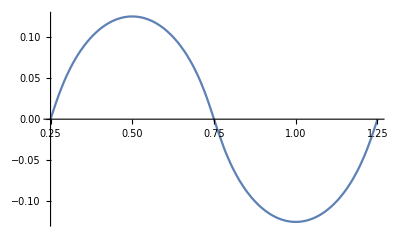

1.

```mathematica
(* write your code here *)
(*set up constants*)
m = 0.03
q = 0.2*10^(-6)
Q = -1*10^(-6)
x1not = -0.1255
v1not = 0
x1 = {x, y}
x2 = {0, 0.05}
k = 8.99*10^9

(*define potential energy and force*)
U = k*q*Q/Sqrt[(x1[[1]] - x2[[1]])^2 + (x1[[2]] - x2[[2]])^2]
F = -Grad[U, {x, y}]
(*set up differential equations and initial conditions
Note that we only need to use one of the equations since
the particle is constrained to move along the x axis
*)
vals ={x ->x[t], y->0}
F = F/.vals
eq1 = m*x''[t] == F[[1]]
IC = {x[0]==x1not, x'[0]==v1not}
(*solve and plot*)
sol = NDSolve[{eq1, IC}, {x}, {t, 0, 3}]

Plot[Evaluate[x[t]/.sol],{t,0.250,1.250}]
(*first crosses the t axis at about 0.25 seconds*)
(*and then again at 1.250 seconds*)
(*so the period of oscillation is 1.3252 - 0.265041*)
T = 1.250 - 0.250
```

The period of oscillation is: 1 second

## Additional work for any of the written problems (label each one clearly)

Work for problem 1:

```mathematica
V = q*{vx, vy, vz};V//MatrixForm
Bm = {0, 0, B};B//MatrixForm
Cross[V, Bm]
```

(q vx
q vy
q vz)

B

{B q vy,-B q vx,0}

Work for problem 3:

```mathematica
U = m*g*((r+b)*Cos[θ] + r*θ*Sin[θ]);
D1 =FullSimplify[D[U, θ]];
D2 = FullSimplify[D[D1, θ]]
FullSimplify[D2/.{θ->0}]
```

-g m ((b-r) Cos[θ]+r θ Sin[θ])

g m (-b+r)

Work for problem 5

```mathematica
Quit[]
Clear["`*"]
```

```mathematica
rvec = {x, y, L}
rdotvec = {xdot, ydot, zdot}
OmegaVec = Ω*{0, 0, 1}
Tx = -m*g*x/L
Ty = -m*g*y/L

FullSimplify[m*xddot==Tx + m*Cross[Cross[OmegaVec, rvec], OmegaVec] [[1]] +2*m*Cross[rdotvec, OmegaVec] [[1]] ]
FullSimplify[m*yddot==Tx + m*Cross[Cross[OmegaVec, rvec], OmegaVec] [[2]] +2*m*Cross[rdotvec, OmegaVec] [[2]] ]
```

{x,y,L}

{xdot,ydot,zdot}

{0,0,Ω}

-(g m x)/L

-(g m y)/L

m ((g x)/L+xddot-Ω (2 ydot+x Ω))==0

m ((g x)/L+yddot+Ω (2 xdot-y Ω))==0

Work for problem 6

```mathematica
U = -γ/Sqrt[x^2 + y^2 + z^2]
F = -Grad[U, {x,y, z}]
Curl[F, {x, y, z}]
r1 = {-15/4, 39/20, 0};
r2 = {5/2, -13/10, 0};
v1 = {9, -15/4, 0};
v2 = {-6, 2.5, 0};
m1 = 1
m2 = 3/2
p1 = m1*v1;
p2 = m2*v2;
Print["CM:"]
1/(m1 + m2)*(m1*r1 + m2*r2)
Print["Momentum:"]
p1 + p2

Print["angular momentum:"]
L = Cross[r1, p1] + Cross[r2, p2];L//MatrixForm
r = Norm[r1 - r2];
mu = m1*m2/(m1 + m2)
rdot = Norm[v1 - v2]^2

Print["Energy:"]
En = mu*rdot^2/2 + mu*r^2*(Norm[L]/(mu*r^2))^2/2 + -1000/r
```

-γ/(√(x^2+y^2+z^2))

{-(x γ)/((x^2+y^2+z^2)^(3/2)),-(y γ)/((x^2+y^2+z^2)^(3/2)),-(z γ)/((x^2+y^2+z^2)^(3/2))}

{0,0,0}

1

3/2

CM:

{0,0,0}

Momentum:

{0,0.,0}

angular momentum:

(0.
0
-5.8125)

3/5

264.063

Energy:

20777.3

Work for exercise 8

```mathematica
lambda= 3*m/(2*L)*(1 - (s/L)^2)
rperp2 = (s*Cos[θ])^2
Irod = FullSimplify[Integrate[ lambda* rperp2, {s, 0, L}]]
Ibob = m*(L*Cos[θ])^2
Itotal = FullSimplify[Irod + Ibob]
CMrod = FullSimplify[Integrate[s*lambda /m, {s, 0, L}]]
CMpend = 1/(2*m)*(CMrod*m + L*m)
```

(3 m (1-s^2/L^2))/(2 L)

s^2 Cos[θ]^2

1/5 L^2 m Cos[θ]^2

L^2 m Cos[θ]^2

6/5 L^2 m Cos[θ]^2

(3 L)/8

(11 L)/16